```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];(*Get["HopfE`"];*)
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[k1]:=Subscript[k,d];Format[k2]:=Subscript[k,g];
Format[muS]:=Subscript[μ,s];Format[laS]:=Subscript[θ,2];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;Format[muB]:=Subscript[μ,b];Format[muC]:=Subscript[μ,c];
Format[La]:=Λ;Format[beC]:=Subscript[β,c];Format[be2]:=Subscript[β,2];
Format[beB]:=Subscript[β,b];
RN = {
  0 -> "S",
  "S" -> 0,
  "S" + "B" -> 2*"B",
  "B" -> 0,
  "S" + "C" -> 2*"C",
  "C" -> 0,
  "D" -> "G",
  "G" -> "D"
}

rts = {
  La,       (* birth S *)
  muS*S,         (* death S *)
  beB*S*B,     (* inf. B *)
  muB*B,         (* death B *)
  beC*S*C,     (* inf. C *)
  muC*C,         (* death C *)
  k1*D,          (* D->E *)
  k2*G           (* E->D *)
};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)

{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
RHS//MatrixForm
Print["siphons are",mSi,"E0 is",E0," R1,R2, ... are",R0A/.E0]
jac=Grad[RHS,var];K//MatrixForm
ng[[2]]//MatrixForm
ng[[3]]//MatrixForm
var.cons[gam]
```

{0→S,S→0,B+S→2 B,B→0,C+S→2 C,C→0,D→G,G→D}

reactions and transitions: (0→S | Λ
S→0 | μ_s S
B+S→2 B | B β_b S
B→0 | B μ_b
C+S→2 C | β_c C S
C→0 | C μ_c
D→G | D k_d
G→D | G k_g)

Singular case

(Λ-B β_b S-β_c C S-μ_s S
-B μ_b+B β_b S
-C μ_c+β_c C S
-D k_d+G k_g
D k_d-G k_g)

siphons are{{B},{C},{D,G}}E0 is{S→Λ/μ_s,B→0,C→0,D→0,G→0} R1,R2, ... areEigenvalues[singular]

singular

(β_b S | 0 | 0 | 0
0 | β_c S | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(μ_b | 0 | 0 | 0
0 | μ_c | 0 | 0
0 | 0 | k_d | -k_g
0 | 0 | -k_d | k_g)

Dot::dotsh: Tensors {S,B,C,D,G} and {{0,0,0,1,1}} have incompatible shapes.

{S,B,C,D,G}.{{0,0,0,1,1}}

```mathematica
mod={RHS,var,par};inf={I1,II2,I2};


bdfp=bdFp[RHS,var,mSi]
(*ng=NGM[mod,inf];
F=ng[[2]];F//MatrixForm
V=ng[[3]];V//MatrixForm
K=ng[[4]];K//MatrixForm*)
```

```mathematica
(*E1*)
cE1=bdfp[[2]][[1]][[1]];po2=Collect[bdfp[[1]][[2]]/i2,i2];
{R12,R21,coP}=invN[cE1,F,R0A,E0,par,cp];
j1=jac/.cE1/.i2->0//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
Print["Stability of E1 holds iff R12 <1"]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

reactions and transitions: (0→S | muS
S→0 | muS S
I1+S→2 I1 | beta1 I1 S
I2+S→2 I2 | beta2 I2 S
I12+S→2 I12 | beta12 I12 S
I12→I1 | I12 m21
I12→I2 | I12 m2
I1+I2→I12 | delta I1 I2
I1→0 | I1 mu1
I2→0 | I2 mu2
I12→0 | I12 mu12)

```mathematica
{muS-beta1 I1 S-be12 I3 S-be2 I2 S-muS S,-delta I1 I2+I3 m1-I1 mu1+beta1 I1 S,-delta I1 I2+I3 m2-I2 mu2+be2 I2 S,delta I1 I2-I3 m2-I3 m1-I3 mu12+be12 I3 S}
```

siphons are{{I1,I12},{I2,I12}}E0 is{S→1,I1→0,I12→0,I2→0} R1,R2 are{beta2/mu2,beta12/(m2+m21+mu12),beta1/mu1}

fps on siphon facet {I1,I12}: 2 boundary points

fps on siphon facet {I2,I12}: 2 boundary points

```mathematica
{{{{I2->0,S->1},{I2->((be2-mu2) muS)/(be2 mu2),S->mu2/be2}},EpidCRN`Private`AllSolsRational},{{{I1->0,S->1},{I1->((beta1-mu1) muS)/(beta1 mu1),S->mu1/beta1}},EpidCRN`Private`AllSolsRational}}
```

R0A has 3 elements

Invasion numbers: R12 = beta12/(m2+m21+mu12), R21 = nonRat

At least one equilibrium irrational - coexistence analysis not possible

At cE1, chp of jac, ch1, factorizes as

```mathematica
-be12 be2 delta I3 I2 m1-be12 be2 I3 m1 mu1+beta1 be12 be2 I3 mu12-be12 be2 delta I3 I2 mu12-be12 be2 I3 mu1 mu12+beta1 be12 be2 I2 mu2-be12 be2 delta I2^2 mu2-beta1 be12 I3 m2 mu2-beta1 be2 I2 m2 mu2+be12 delta I3 I2 m2 mu2+be2 delta I2^2 m2 mu2-beta1 be2 I2 m1 mu2-be12 be2 I2 mu1 mu2+be12 I3 m2 mu1 mu2+be2 I2 m2 mu1 mu2+be12 I3 m1 mu1 mu2+be2 I2 m1 mu1 mu2-beta1 be12 I3 mu12 mu2-beta1 be2 I2 mu12 mu2+be12 delta I3 I2 mu12 mu2+be2 delta I2^2 mu12 mu2+be12 I3 mu1 mu12 mu2+be2 I2 mu1 mu12 mu2-beta1 be12 be2 muS+be12 be2 delta I2 muS+beta1 be2 m2 muS-be2 delta I2 m2 muS+beta1 be2 m1 muS+be12 be2 mu1 muS-be2 m2 mu1 muS-be2 m1 mu1 muS+beta1 be2 mu12 muS-be2 delta I2 mu12 muS-be2 mu1 mu12 muS+beta1 be12 mu2 muS-be12 delta I2 mu2 muS-beta1 m2 mu2 muS+delta I2 m2 mu2 muS-beta1 m1 mu2 muS-be12 mu1 mu2 muS+m2 mu1 mu2 muS+m1 mu1 mu2 muS-beta1 mu12 mu2 muS+delta I2 mu12 mu2 muS+mu1 mu12 mu2 muS-beta1 be12 be2 u+beta1 be12 be2 I3 u+beta1 be12 be2 I2 u+be12 be2 delta I2 u-be12 be2 delta I3 I2 u-be12 be2 delta I2^2 u+beta1 be2 m2 u-beta1 be12 I3 m2 u-beta1 be2 I2 m2 u-be2 delta I2 m2 u+be12 delta I3 I2 m2 u+be2 delta I2^2 m2 u+beta1 be2 m1 u-be12 be2 I3 m1 u-beta1 be2 I2 m1 u+be12 be2 mu1 u-be12 be2 I3 mu1 u-be12 be2 I2 mu1 u-be2 m2 mu1 u+be12 I3 m2 mu1 u+be2 I2 m2 mu1 u-be2 m1 mu1 u+be12 I3 m1 mu1 u+be2 I2 m1 mu1 u+beta1 be2 mu12 u-beta1 be12 I3 mu12 u-be12 be2 I3 mu12 u-beta1 be2 I2 mu12 u-be2 delta I2 mu12 u+be12 delta I3 I2 mu12 u+be2 delta I2^2 mu12 u-be2 mu1 mu12 u+be12 I3 mu1 mu12 u+be2 I2 mu1 mu12 u+beta1 be12 mu2 u-beta1 be12 I3 mu2 u-beta1 be2 I2 mu2 u-be12 be2 I2 mu2 u-be12 delta I2 mu2 u+be12 delta I3 I2 mu2 u+be2 delta I2^2 mu2 u-beta1 m2 mu2 u+be12 I3 m2 mu2 u+be2 I2 m2 mu2 u+delta I2 m2 mu2 u-beta1 m1 mu2 u+be12 I3 m1 mu2 u+be2 I2 m1 mu2 u-be12 mu1 mu2 u+be12 I3 mu1 mu2 u+be2 I2 mu1 mu2 u+m2 mu1 mu2 u+m1 mu1 mu2 u-beta1 mu12 mu2 u+be12 I3 mu12 mu2 u+be2 I2 mu12 mu2 u+delta I2 mu12 mu2 u+mu1 mu12 mu2 u+beta1 be12 muS u+beta1 be2 muS u+be12 be2 muS u-be12 delta I2 muS u-be2 delta I2 muS u-beta1 m2 muS u-be2 m2 muS u+delta I2 m2 muS u-beta1 m1 muS u-be2 m1 muS u-be12 mu1 muS u-be2 mu1 muS u+m2 mu1 muS u+m1 mu1 muS u-beta1 mu12 muS u-be2 mu12 muS u+delta I2 mu12 muS u+mu1 mu12 muS u-beta1 mu2 muS u-be12 mu2 muS u+delta I2 mu2 muS u+m2 mu2 muS u+m1 mu2 muS u+mu1 mu2 muS u+mu12 mu2 muS u+beta1 be12 u^2+beta1 be2 u^2+be12 be2 u^2-beta1 be12 I3 u^2-be12 be2 I3 u^2-beta1 be2 I2 u^2-be12 be2 I2 u^2-be12 delta I2 u^2-be2 delta I2 u^2+be12 delta I3 I2 u^2+be2 delta I2^2 u^2-beta1 m2 u^2-be2 m2 u^2+be12 I3 m2 u^2+be2 I2 m2 u^2+delta I2 m2 u^2-beta1 m1 u^2-be2 m1 u^2+be12 I3 m1 u^2+be2 I2 m1 u^2-be12 mu1 u^2-be2 mu1 u^2+be12 I3 mu1 u^2+be2 I2 mu1 u^2+m2 mu1 u^2+m1 mu1 u^2-beta1 mu12 u^2-be2 mu12 u^2+be12 I3 mu12 u^2+be2 I2 mu12 u^2+delta I2 mu12 u^2+mu1 mu12 u^2-beta1 mu2 u^2-be12 mu2 u^2+be12 I3 mu2 u^2+be2 I2 mu2 u^2+delta I2 mu2 u^2+m2 mu2 u^2+m1 mu2 u^2+mu1 mu2 u^2+mu12 mu2 u^2-beta1 muS u^2-be12 muS u^2-be2 muS u^2+delta I2 muS u^2+m2 muS u^2+m1 muS u^2+mu1 muS u^2+mu12 muS u^2+mu2 muS u^2-beta1 u^3-be12 u^3-be2 u^3+be12 I3 u^3+be2 I2 u^3+delta I2 u^3+m2 u^3+m1 u^3+mu1 u^3+mu12 u^3+mu2 u^3+muS u^3+u^4
```

Stability of E1 holds iff R12 <1

```mathematica
(*EE*)
eq=Thread[RHS==0];so=Solve[eq,var];
Print["There are ",so//Length," fps "]
cEE=so[[2]]//FullSimplify
Print["Existence of EE holds iff R1>R2,  R12 <1, R21<1"]
reE=Reduce[Join[cp,Thread[(var/.cEE)>=0]]]//FullSimplify
jE=jac/.cEE//FullSimplify;
Print[" At cEE, chp of jac, chE, factorizes as"]
chE=Numerator[Together[CharacteristicPolynomial[jE,u]]]//Factor
```

There are 5 fps

{s→μ_1/β_1,i_1→Λ/μ_1+(-μ+(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(β_2 μ_1-β_1 μ_2),i_2→-μ_v/β_v+(μ_1 ρ)/(-β_2 μ_1+β_1 μ_2),v→(-β_2 μ_1+β_1 μ_2)/(β_1 β_v)}

Existence of EE holds iff R1>R2,  R12 <1, R21<1

μ_2>0&&μ_1>0&&β_2>0&&β_1>(β_2 μ_1)/μ_2&&ρ>0&&μ_v>0&&β_v≥(-β_2 μ_1 μ_v+β_1 μ_2 μ_v)/(μ_1 ρ)&&μ>0&&Λ≥μ_1 ((μ-(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(-β_2 μ_1+β_1 μ_2))

At cEE, chp of jac, chE, factorizes as

β_1 β_2^3 β_v Λ μ_1^4 μ_v-β_2^3 β_v μ μ_1^5 μ_v-3 β_1^2 β_2^2 β_v Λ μ_1^3 μ_2 μ_v+3 β_1 β_2^2 β_v μ μ_1^4 μ_2 μ_v+3 β_1^3 β_2 β_v Λ μ_1^2 μ_2^2 μ_v-3 β_1^2 β_2 β_v μ μ_1^3 μ_2^2 μ_v-β_1^4 β_v Λ μ_1 μ_2^3 μ_v+β_1^3 β_v μ μ_1^2 μ_2^3 μ_v+β_2^4 μ_1^5 μ_v^2-3 β_1 β_2^3 μ_1^4 μ_2 μ_v^2+3 β_1^2 β_2^2 μ_1^3 μ_2^2 μ_v^2-β_1^3 β_2 μ_1^2 μ_2^3 μ_v^2+β_1 β_2^2 β_v^2 Λ μ_1^4 ρ-β_2^2 β_v^2 μ μ_1^5 ρ-2 β_1^2 β_2 β_v^2 Λ μ_1^3 μ_2 ρ+2 β_1 β_2 β_v^2 μ μ_1^4 μ_2 ρ+β_1^3 β_v^2 Λ μ_1^2 μ_2^2 ρ-β_1^2 β_v^2 μ μ_1^3 μ_2^2 ρ+β_2^3 β_v μ_1^5 μ_v ρ-β_1 β_2^2 β_v μ_1^4 μ_2 μ_v ρ-β_1^2 β_2 β_v μ_1^3 μ_2^2 μ_v ρ+β_1^3 β_v μ_1^2 μ_2^3 μ_v ρ+β_1 β_2 β_v^2 μ_1^4 μ_2 ρ^2-β_1^2 β_v^2 μ_1^3 μ_2^2 ρ^2+β_1 β_2^3 β_v Λ μ_1^3 μ_v u-3 β_1^2 β_2^2 β_v Λ μ_1^2 μ_2 μ_v u+3 β_1^3 β_2 β_v Λ μ_1 μ_2^2 μ_v u-β_1^4 β_v Λ μ_2^3 μ_v u-β_1^2 β_2 β_v^2 Λ μ_1^3 ρ u+β_1 β_2^2 β_v^2 Λ μ_1^3 ρ u+β_1 β_2 β_v^2 μ μ_1^4 ρ u+β_1^3 β_v^2 Λ μ_1^2 μ_2 ρ u-2 β_1^2 β_2 β_v^2 Λ μ_1^2 μ_2 ρ u-β_1^2 β_v^2 μ μ_1^3 μ_2 ρ u+β_1^3 β_v^2 Λ μ_1 μ_2^2 ρ u-β_1 β_2^2 β_v μ_1^4 μ_v ρ u+β_1^2 β_2 β_v μ_1^3 μ_2 μ_v ρ u+β_1 β_2^2 β_v μ_1^3 μ_2 μ_v ρ u-β_1^2 β_2 β_v μ_1^2 μ_2^2 μ_v ρ u-β_1^2 β_v^2 μ_1^3 μ_2 ρ^2 u+β_1 β_2 β_v^2 μ_1^3 μ_2 ρ^2 u+β_1^2 β_2^2 β_v Λ μ_1^3 u^2-β_1 β_2^2 β_v μ μ_1^4 u^2-2 β_1^3 β_2 β_v Λ μ_1^2 μ_2 u^2+2 β_1^2 β_2 β_v μ μ_1^3 μ_2 u^2+β_1^4 β_v Λ μ_1 μ_2^2 u^2-β_1^3 β_v μ μ_1^2 μ_2^2 u^2+β_1 β_2^3 μ_1^4 μ_v u^2-β_2^4 μ_1^4 μ_v u^2+β_2^3 β_v μ_1^4 μ_v u^2-2 β_1^2 β_2^2 μ_1^3 μ_2 μ_v u^2+2 β_1 β_2^3 μ_1^3 μ_2 μ_v u^2-3 β_1 β_2^2 β_v μ_1^3 μ_2 μ_v u^2+β_1^3 β_2 μ_1^2 μ_2^2 μ_v u^2-β_1^2 β_2^2 μ_1^2 μ_2^2 μ_v u^2+3 β_1^2 β_2 β_v μ_1^2 μ_2^2 μ_v u^2-β_1^3 β_v μ_1 μ_2^3 μ_v u^2-β_1^2 β_2 β_v^2 Λ μ_1^2 ρ u^2-β_2^3 β_v μ_1^4 ρ u^2+β_2^2 β_v^2 μ_1^4 ρ u^2+β_1^3 β_v^2 Λ μ_1 μ_2 ρ u^2+β_1^2 β_2 β_v μ_1^3 μ_2 ρ u^2+β_1 β_2^2 β_v μ_1^3 μ_2 ρ u^2-2 β_1 β_2 β_v^2 μ_1^3 μ_2 ρ u^2-β_1^3 β_v μ_1^2 μ_2^2 ρ u^2+β_1^2 β_v^2 μ_1^2 μ_2^2 ρ u^2+β_1^2 β_2^2 β_v Λ μ_1^2 u^3-2 β_1^3 β_2 β_v Λ μ_1 μ_2 u^3+β_1^4 β_v Λ μ_2^2 u^3-β_1 β_2 β_v^2 μ_1^3 ρ u^3+β_1^2 β_v^2 μ_1^2 μ_2 ρ u^3+β_1 β_2^2 β_v μ_1^3 u^4-2 β_1^2 β_2 β_v μ_1^2 μ_2 u^4+β_1^3 β_v μ_1 μ_2^2 u^4

```mathematica
(*E2*)c1=Thread[mSi[[1]]->0];
RH2=remZ[RHS/.c1//FullSimplify];RH2[[2]]=(RHS/.c1)[[3]]/i2//Factor
RH2
so=Solve[Thread[RH2[[{1,3}]]==0],{s,v}]//Flatten
co=FullSimplify/@CoefficientList[po2,i2]
pc=co[[1]]<0||(co[[1]]>=0&&co[[2]]^2-4 co[[1]]*co[[3]]<0);
(*re=Reduce[Append[cp,co[[1]]<=0]]//FullSimplify
re=Reduce[Append[cp,pc]]//FullSimplify ; funny answers*)
```

-μ_2+β_2 s+β_v v

{Λ-(β_2 i_2+μ+ρ) s,-μ_2+β_2 s+β_v v,ρ s-(β_v i_2+μ_v) v}

{s→Λ/(β_2 i_2+μ+ρ),v→(Λ ρ)/((β_v i_2+μ_v) (β_2 i_2+μ+ρ))}

{-β_2 Λ μ_v-β_v Λ ρ+μ_2 μ_v (μ+ρ),β_2 (-β_v Λ+μ_2 μ_v)+β_v μ_2 (μ+ρ),β_2 β_v μ_2}

```mathematica
j2=jac/.so/.i1->0//FullSimplify;
Print[" At cE2, chp of jac, ch2, factorizes as"]
ch2=Numerator[Together[CharacteristicPolynomial[j2,u]]]//Factor
List@@ch2//Length
{lSta,qSta,hDeg,ll,ql}=sta[ch2]
```

At cE2, chp of jac, ch2, factorizes as

(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2-2 β_2 i_2 μ μ_2 μ_v^2-μ^2 μ_2 μ_v^2-2 β_2 β_v^2 i_2^3 μ_2 ρ-2 β_v^2 i_2^2 μ μ_2 ρ+2 β_2 β_v i_2 Λ μ_v ρ+β_v Λ μ μ_v ρ-4 β_2 β_v i_2^2 μ_2 μ_v ρ-4 β_v i_2 μ μ_2 μ_v ρ+β_2 Λ μ_v^2 ρ-2 β_2 i_2 μ_2 μ_v^2 ρ-2 μ μ_2 μ_v^2 ρ-β_v^2 i_2^2 μ_2 ρ^2+β_v Λ μ_v ρ^2-2 β_v i_2 μ_2 μ_v ρ^2-μ_2 μ_v^2 ρ^2-β_2^2 β_v^2 i_2^4 u+β_2 β_v^2 i_2^2 Λ u-2 β_2 β_v^2 i_2^3 μ u+β_2 β_v i_2 Λ μ u-β_v^2 i_2^2 μ^2 u-β_2^2 β_v i_2^3 μ_2 u-β_2 β_v^2 i_2^3 μ_2 u-2 β_2 β_v i_2^2 μ μ_2 u-β_v^2 i_2^2 μ μ_2 u-β_v i_2 μ^2 μ_2 u-2 β_2^2 β_v i_2^3 μ_v u+2 β_2 β_v i_2 Λ μ_v u-4 β_2 β_v i_2^2 μ μ_v u+β_2 Λ μ μ_v u-2 β_v i_2 μ^2 μ_v u-β_2^2 i_2^2 μ_2 μ_v u-2 β_2 β_v i_2^2 μ_2 μ_v u-2 β_2 i_2 μ μ_2 μ_v u-2 β_v i_2 μ μ_2 μ_v u-μ^2 μ_2 μ_v u-β_2^2 i_2^2 μ_v^2 u+β_2 Λ μ_v^2 u-2 β_2 i_2 μ μ_v^2 u-μ^2 μ_v^2 u-β_2 i_2 μ_2 μ_v^2 u-μ μ_2 μ_v^2 u-2 β_2 β_v^2 i_2^3 ρ u+2 β_2 β_v i_2 Λ ρ u-2 β_v^2 i_2^2 μ ρ u+β_v Λ μ ρ u-2 β_2 β_v i_2^2 μ_2 ρ u-β_v^2 i_2^2 μ_2 ρ u-2 β_v i_2 μ μ_2 ρ u-4 β_2 β_v i_2^2 μ_v ρ u+β_2 Λ μ_v ρ u+β_v Λ μ_v ρ u-4 β_v i_2 μ μ_v ρ u-2 β_2 i_2 μ_2 μ_v ρ u-2 β_v i_2 μ_2 μ_v ρ u-2 μ μ_2 μ_v ρ u-2 β_2 i_2 μ_v^2 ρ u-2 μ μ_v^2 ρ u-μ_2 μ_v^2 ρ u-β_v^2 i_2^2 ρ^2 u+β_v Λ ρ^2 u-β_v i_2 μ_2 ρ^2 u-2 β_v i_2 μ_v ρ^2 u-μ_2 μ_v ρ^2 u-μ_v^2 ρ^2 u-β_2^2 β_v i_2^3 u^2-β_2 β_v^2 i_2^3 u^2+β_2 β_v i_2 Λ u^2-2 β_2 β_v i_2^2 μ u^2-β_v^2 i_2^2 μ u^2-β_v i_2 μ^2 u^2-β_2 β_v i_2^2 μ_2 u^2-β_v i_2 μ μ_2 u^2-β_2^2 i_2^2 μ_v u^2-2 β_2 β_v i_2^2 μ_v u^2+β_2 Λ μ_v u^2-2 β_2 i_2 μ μ_v u^2-2 β_v i_2 μ μ_v u^2-μ^2 μ_v u^2-β_2 i_2 μ_2 μ_v u^2-μ μ_2 μ_v u^2-β_2 i_2 μ_v^2 u^2-μ μ_v^2 u^2-2 β_2 β_v i_2^2 ρ u^2-β_v^2 i_2^2 ρ u^2+β_v Λ ρ u^2-2 β_v i_2 μ ρ u^2-β_v i_2 μ_2 ρ u^2-2 β_2 i_2 μ_v ρ u^2-2 β_v i_2 μ_v ρ u^2-2 μ μ_v ρ u^2-μ_2 μ_v ρ u^2-μ_v^2 ρ u^2-β_v i_2 ρ^2 u^2-μ_v ρ^2 u^2-β_2 β_v i_2^2 u^3-β_v i_2 μ u^3-β_2 i_2 μ_v u^3-μ μ_v u^3-β_v i_2 ρ u^3-μ_v ρ u^3)

2

Set::shape: Lists {lSta,qSta,hDeg,ll,ql} and sta[(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2+«100»)] are not the same shape.

sta[(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2-2 β_2 i_2 μ μ_2 μ_v^2-μ^2 μ_2 μ_v^2-2 β_2 β_v^2 i_2^3 μ_2 ρ-2 β_v^2 i_2^2 μ μ_2 ρ+2 β_2 β_v i_2 Λ μ_v ρ+β_v Λ μ μ_v ρ-4 β_2 β_v i_2^2 μ_2 μ_v ρ-4 β_v i_2 μ μ_2 μ_v ρ+β_2 Λ μ_v^2 ρ-2 β_2 i_2 μ_2 μ_v^2 ρ-2 μ μ_2 μ_v^2 ρ-β_v^2 i_2^2 μ_2 ρ^2+β_v Λ μ_v ρ^2-2 β_v i_2 μ_2 μ_v ρ^2-μ_2 μ_v^2 ρ^2-β_2^2 β_v^2 i_2^4 u+β_2 β_v^2 i_2^2 Λ u-2 β_2 β_v^2 i_2^3 μ u+β_2 β_v i_2 Λ μ u-β_v^2 i_2^2 μ^2 u-β_2^2 β_v i_2^3 μ_2 u-β_2 β_v^2 i_2^3 μ_2 u-2 β_2 β_v i_2^2 μ μ_2 u-β_v^2 i_2^2 μ μ_2 u-β_v i_2 μ^2 μ_2 u-2 β_2^2 β_v i_2^3 μ_v u+2 β_2 β_v i_2 Λ μ_v u-4 β_2 β_v i_2^2 μ μ_v u+β_2 Λ μ μ_v u-2 β_v i_2 μ^2 μ_v u-β_2^2 i_2^2 μ_2 μ_v u-2 β_2 β_v i_2^2 μ_2 μ_v u-2 β_2 i_2 μ μ_2 μ_v u-2 β_v i_2 μ μ_2 μ_v u-μ^2 μ_2 μ_v u-β_2^2 i_2^2 μ_v^2 u+β_2 Λ μ_v^2 u-2 β_2 i_2 μ μ_v^2 u-μ^2 μ_v^2 u-β_2 i_2 μ_2 μ_v^2 u-μ μ_2 μ_v^2 u-2 β_2 β_v^2 i_2^3 ρ u+2 β_2 β_v i_2 Λ ρ u-2 β_v^2 i_2^2 μ ρ u+β_v Λ μ ρ u-2 β_2 β_v i_2^2 μ_2 ρ u-β_v^2 i_2^2 μ_2 ρ u-2 β_v i_2 μ μ_2 ρ u-4 β_2 β_v i_2^2 μ_v ρ u+β_2 Λ μ_v ρ u+β_v Λ μ_v ρ u-4 β_v i_2 μ μ_v ρ u-2 β_2 i_2 μ_2 μ_v ρ u-2 β_v i_2 μ_2 μ_v ρ u-2 μ μ_2 μ_v ρ u-2 β_2 i_2 μ_v^2 ρ u-2 μ μ_v^2 ρ u-μ_2 μ_v^2 ρ u-β_v^2 i_2^2 ρ^2 u+β_v Λ ρ^2 u-β_v i_2 μ_2 ρ^2 u-2 β_v i_2 μ_v ρ^2 u-μ_2 μ_v ρ^2 u-μ_v^2 ρ^2 u-β_2^2 β_v i_2^3 u^2-β_2 β_v^2 i_2^3 u^2+β_2 β_v i_2 Λ u^2-2 β_2 β_v i_2^2 μ u^2-β_v^2 i_2^2 μ u^2-β_v i_2 μ^2 u^2-β_2 β_v i_2^2 μ_2 u^2-β_v i_2 μ μ_2 u^2-β_2^2 i_2^2 μ_v u^2-2 β_2 β_v i_2^2 μ_v u^2+β_2 Λ μ_v u^2-2 β_2 i_2 μ μ_v u^2-2 β_v i_2 μ μ_v u^2-μ^2 μ_v u^2-β_2 i_2 μ_2 μ_v u^2-μ μ_2 μ_v u^2-β_2 i_2 μ_v^2 u^2-μ μ_v^2 u^2-2 β_2 β_v i_2^2 ρ u^2-β_v^2 i_2^2 ρ u^2+β_v Λ ρ u^2-2 β_v i_2 μ ρ u^2-β_v i_2 μ_2 ρ u^2-2 β_2 i_2 μ_v ρ u^2-2 β_v i_2 μ_v ρ u^2-2 μ μ_v ρ u^2-μ_2 μ_v ρ u^2-μ_v^2 ρ u^2-β_v i_2 ρ^2 u^2-μ_v ρ^2 u^2-β_2 β_v i_2^2 u^3-β_v i_2 μ u^3-β_2 i_2 μ_v u^3-μ μ_v u^3-β_v i_2 ρ u^3-μ_v ρ u^3)]

```mathematica
re=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

ρ>0&&μ>0&&μ_1>0&&Λ>0&&μ_v>0&&μ_2>0&&β_v>0&&β_2>0&&μ_1 (μ+ρ)<β_1 Λ&&β_2 μ_1 μ_v+β_v μ_1 ρ<β_1 μ_2 μ_v

```mathematica
j1=jac/.cE1/.i2->0//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
Apart/@SolveValues[ch1==0,u]
{lSta,qSta,hDeg,ll,ql}=sta[ch1]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

There are 5 fps

{s→μ_1/β_1,i_1→Λ/μ_1+(-μ+(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(β_2 μ_1-β_1 μ_2),i_2→-μ_v/β_v+(μ_1 ρ)/(-β_2 μ_1+β_1 μ_2),v→(-β_2 μ_1+β_1 μ_2)/(β_1 β_v)}

```mathematica
so4=so[[4]]//FullSimplify
```

{s→(β_2 (-β_v Λ+μ_2 μ_v)-β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 (-β_v μ+β_2 μ_v)),i_1→0,i_2→(β_2 (β_v Λ-μ_2 μ_v)-β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 β_v μ_2),v→(-β_2 (β_v Λ+μ_2 μ_v)+β_v μ_2 (μ-ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_v (β_v μ-β_2 μ_v))}

```mathematica
so5=so[[5]]//FullSimplify
```

{s→(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 (β_v μ-β_2 μ_v)),i_1→0,i_2→-(-β_2 β_v Λ+β_v μ μ_2+β_2 μ_2 μ_v+β_v μ_2 ρ+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 β_v μ_2),v→-(β_2 β_v Λ-β_v μ μ_2+β_2 μ_2 μ_v+β_v μ_2 ρ+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_v (β_v μ-β_2 μ_v))}

Checked 513 potential coexistence points

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

DFE: 140 (2%)

E2: 2369 (40%)

E1: 2937 (49%)

EE-Stable: 513 (9%)

{11.5313,Null}

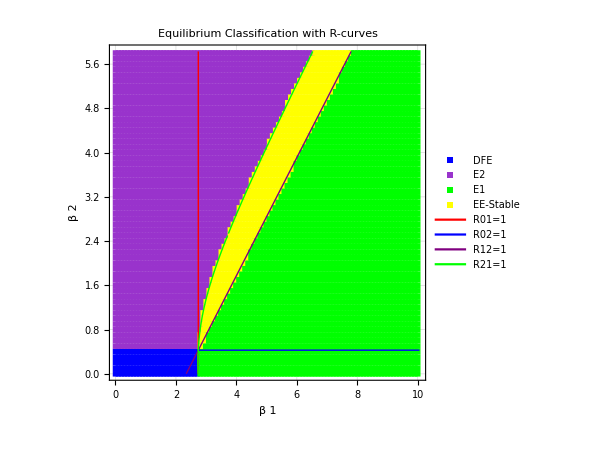

```mathematica
plotInd={1,2};varInd={1,2,3};p0val=par/.coP;steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[{fPl,unC,res}=scan[RHS,var,par,p0val,plotInd,varInd,Automatic,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]
fPl
```

```mathematica
Export["LiScan.pdf",fPl]
```

LiScan.pdf